# Deep Learning for Text Analysis

## Exercises

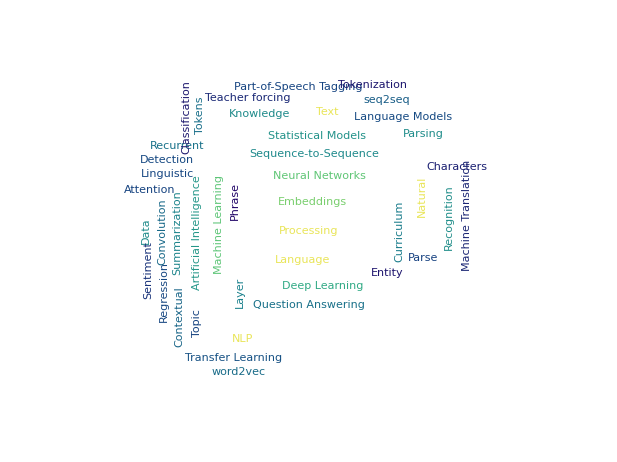

## Multiple-Choice Questions

Underline the correct answers to the following questions.

### NLP Applications

Tokenization in ELMo model splits text into:

Characters

Subwords

Words

Sentences

Tokenization in BERT model splits text into:

Characters

Subwords

Words

Sentences

NLP application(s) that need to know the positions of the tokens are:

Sentence entailment

Question answering (from an unstructured collection of natural language documents)

Named entity recognition

Text classification tasks (sentiment analysis, topic labeling, language identification)

### Deep Learning

Which of these net layer(s) allows taking into account the context of a word in a text of variable length?

LinearLayer (fully connected)

ConvolutionLayer

LongShortTermMemoryLayer

GatedRecurrentUnit

AttentionLayer

When applied directly to word embeddings, which of these net layer(s) allows directly applying weights to n-gram of words?

Note: n-gram is a contiguous sequence of n items from a given sample of text.

LinearLayer (fully connected)

ConvolutionLayer

LongShortTermMemoryLayer

GatedRecurrentUnit

AttentionLayer

The last output layer of a pointer network should be:

ConvolutionLayer

ElementwiseLayer[LogisticSigmoid]

SoftmaxLayer

AttentionLayer

Which of these layers can allow handling two text inputs?

ConvolutionLayer

LongShortTermMemoryLayer

GatedRecurrentUnit

AttentionLayer

NetPairEmbeddingOperator

Which of the following methods can be used as a regularization method?

Data augmentation

Cross-validation

Dropout on the activations after nonlinearity

L2 penalty on the weights

### Classic Debugging Cases

Dynamic dimension:

```mathematica
NetInitialize@NetChain[{LongShortTermMemoryLayer[12],LinearLayer[50]}]
```

NetInitialize::valfail: Validation failed for second layer of net (LinearLayer): input port of layer has dimensions ×, but dynamic dimensions are not currently supported by LinearLayer.

$Failed

Why is it failing?

LinearLayer cannot be used with a variable-length sequence input.

LinearLayer input dimensions do not match LongShortTermMemoryLayer output dimensions.

How to fix it?

Map LinearLayer over sequence elements, wrapping LinearLayer inside a NetMapOperator.

LongShortTermMemoryLayer input must be set to a fixed length, for instance, 10: (“Input” -> {10, 5}).

The following network specifications are wrong because:

```mathematica
NetChain[{
	UnitVectorLayer[],
	LongShortTermMemoryLayer[40],
	LongShortTermMemoryLayer[40],
	SequenceLastLayer[],
	LinearLayer[2]
	},
	"Input" -> NetEncoder[{"Characters",{DigitCharacter,"+"}}],
	"Ouput" -> "Real"
	]
```

NetChain::netinvcport: Ouput is neither a valid input or output port for the given NetChain.

$Failed

NetChain forbids the usage of "Output" as a port name specification when the input is a sequence.

A layer’s output is specified twice with mismatch.

There is no way to transform a variable-length input to a real value.

LongShortTermMemoryLayer is repeated twice by mistake.

The network following currently takes an input string and outputs a normalized probability vector for two categories (i.e. “happy”/”sad”). To output the most likely label instead, you should:

```mathematica
NetChain[
	{
	EmbeddingLayer[40],
	DropoutLayer[0.3],
	LongShortTermMemoryLayer[20],
	SequenceLastLayer[],
	LinearLayer[2],
	SoftmaxLayer[]
	},
	"Input" -> NetEncoder[{"Tokens"}]
]
```

NetChain[<>]

Specify the following decoder to the output port: "Output" -> NetDecoder[{"Token", {"happy","sad"}}].

Specify the preceding decoder to the output port and also remove the final SoftmaxLayer.

Specify the following decoder to the output port: "Output" -> NetDecoder[{"Class", {"happy","sad"}}].

Specify the preceding decoder to the output port and also remove the final SoftmaxLayer.

## Make the Machine Learn to Answer Multiple-Choice Questions

Consider a simple question-answering setting where the answer has to be chosen among a limited number of alternatives.

Obtain the bAbI Question-Answering Dataset from the Wolfram Data Repository™.

Make a training dataset and a validation dataset for "Task1" that consist of lists of rules between a pair {statement, rule} and the target.

Hint: One sample in the dataset should look like:
{"Sandra journeyed to the garden. Daniel went to the garden.", "Where is Sandra?"} → "garden"

Collect the set of possible answers and plot a histogram of their counts.

Hint: There are many ways to achieve that. Relevant functions can be DeleteDuplicates, Union, Counts, CountsBy, Histogram, BarChart.

Watch the distribution of the words present in the dataset, using a word cloud and/or bar chart and/or table.

Obtain the BERT net that processes a list of strings from the Wolfram Neural Net Repository™.

Apply BERT on some random text.

Hint: Use MatrixPlot to visualize arrays of numbers.

Note: If you want nets to always output typed NumericArray (instead of List, typically), you can set the following:

<<NeuralNetworks`
NeuralNetworks`$NNOutputHead=NumericArray;

Apply BERT preprocessing (NetEncoder) on some random text.

Hint: Use NetExtract to extract parts of the network.

Hint: Use MatrixForm to visualize arrays of indices.

Precompute the BERT embeddings for the input training and validation data.

Hint: Applying BERT on the training data takes more than two minutes on a GPU and 20 minutes on a CPU. So save them on disk once it is done.

Design a bidirectional recurrent network that takes BERT embeddings and guesses the correct answer.

Hint: Make your network using NetBidirectionalOperator, a recurrent layer from the Neural Network guide.

Hint: Regularize the model with DropoutLayer and/or option "Dropout" of the recurrent layer.

Hint: Attach NetDecoder["Class"] to the output port of the classifier.

Check that you reconstitute a full network that takes a pair of strings (context, question) and returns a string among the possible answers.

Hint: Useful “surgery” functions are NetReplacePart, NetTake, NetJoin, NetAppend, NetFlatten (along with NetGraph).

Train the classifier.

Hint: Do early stopping using the TrainingStoppingCriterion option of NetTrain.

Write a function based on this full network that takes a context, a question, and gives the answer.

Apply the full network to a test sample and modify the input interactively to check the limit of the model generalization.

Choose one of the following paths to continue exploring:

Get similar performance with the smallest net you can.

Explore other models to solve the task as shown in the tutorial on Question Answering.

Solve another task of the bAbI Question-Answering Dataset; solve several tasks with the same model.

## Language Model Net

Background

A language model is a function that contains knowledge about the structure and features of the language (spelling, grammar, usage…). It can be used either to evaluate the realism of a text or to generate a new one based on some criterion (starting text, style, etc.).

Neural nets are powerful tools to learn a language feature, being able to aggregate the information contained in large test corpora available nowadays. In this exploration, you will manipulate such a net, trained to learn English string correlations at the single-character level, to understand how generation, evaluation and training work.

### Generation

Obtain a pretrained language model, Wolfram English Character-Level Language Model V1, from the Wolfram Neural Net Repository™.

Hint: NetModel lets you programmatically query any neural-net-related content from the repository.

Example output:

NetChain[<>]

Test the network on several inputs and for various output types to familiarize yourself with how the NetEncoder and NetDecoder work:

Generating the next most likely character.

Example output:

m

Giving the top 10 most likely next-character probabilities.

Hint: Properties that you can query at net evaluation are given by the NetDecoder attached to the output ports, discoverable through Information[net, "OutputPorts"]. This is presently a NetDecoder[{"Class", …}].

Example outputs:

{m→0.637761,s→0.109947,l→0.0615917}

Giving the net raw output (predicted distribution) and plotting the BarChart of a character’s probabilities.

Example outputs:

{5.44384×10^-31,«95»,2.05236×10^-16}

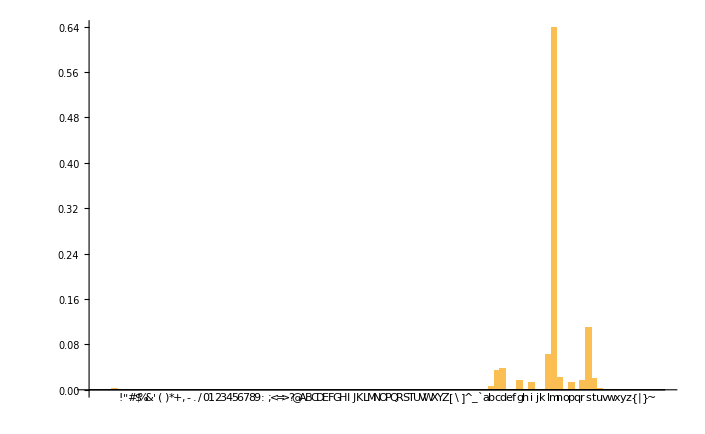

Giving a random sample from the predicted distribution.

Example outputs:

m

Getting both network raw output and recurrent states (this net is a recurrent one) together.

Hint: You can use the special NetPort specification NetPort[All,"States"] to return a list of all recurrent states’ values under this NetPort[All,"States"] key in the output association.

Example outputs:

<|Output→m,NetPort[All,States]→<|«1»|>|>

Verify that you obtain equivalent net raw output in the following cases:

Hint: Typical computation precision in the net is 10*^-6.

Feeding the initial string "Hello" as the input.

Feeding initial string “Hell" as input to obtain net final recurrent states. Then initializing the network states with the values you obtained, feeding them back to port NetPort[All,"States"], together with feeding the additional character "o" to the “Input” port.

Hint: Special NetPort specification NetPort[All,"States"] also works for network input specification.

Using a NetStateObject to maintain the network states between successive evaluations.

Generate some text character by character:

Write a recursive function that takes an initial string and the net, get the next most likely character, append it to the string, and feed the network with the new string until its length reaches a given point. Generate texts.

Example outputs:

Hello, I am sure I am sure you will be able to see you and me and I am sure you will be able to see

The previous function always generates the same output for a given input and is prone to getting stuck in a loop. Can you see why?

Write a new function that samples the next character instead. Now evaluate it several times on different outputs.

Example outputs:

Hello, I asked
her what to get his awe face now. We call for another?"

They turned pitifully and je

(Optional) Rewrite it in the functional way using Nest.

Example outputs:

Hello, I am really the same, now and lunch. He said what you say;
for I do not know he was left, sir. I don't

Both functions are quite slow for long sequences.

Write a new version of the functions taking a initial string and a net or a NetStateObject to have the same result faster.

Note: The computation cost of feeding the whole sequence again and again to the net is eventually p*(p+1)*…*(n-1)*n, where p and n are the initial and final sequence lengths. Most of this computation cost is spent setting the network internal states back to their values after the last sequence.

Hint: Maintaining those states with a NetStateObject between calls, you will only need to provide the new character as input to get the same output result.

Example outputs:

Hello, I am delighting after beleaguered and
help in the mountains that would never make favoured ei

(Optional) Rewrite the code in a functional way using NestList (and NetStateObject).

Example outputs:

Hello, I am sure, wherever Paris? Not unless I am feller of me, and
I believe, how I can say to them

### Likelihood

The net was not trained to perform full sequence probability. Computing the whole sequence probability requires the special tokens StartOfString and EndOfString used as markers at training time and to evaluate:

```mathematica
P["c_1c_2c_3c_4(…c)_N"] = P["c_1"|StartOfString]P["c_2"|"c_1"]P["c_3"|"c_1c_2"]… P[EndOfString|"c_1c_2c_3c_4(…c)_N"]
```

You can, however, rank the likelihood of several candidates for a missing word:

```mathematica
P[leftcontext,"c_1c_2c_3c_4(…c)_N", rightcontext] = P["c_1"|leftcontext]P["c_2"|"c_1", leftcontext]P["c_3"|"c_1c_2", leftcontext]… P[rightcontext|"c_1c_2c_3c_4(…c)_N", leftcontext]
```

Write a function that takes a word "XXX" and evaluate the probability of the sequence: "Hi, do you want to XXX something?". Which of "drink" and "bark" is more likely?

Example outputs:

```mathematica
SeqProba["drink"]
SeqProba["bark"]
```

3.1112×10^-17

4.64092×10^-20

Remove the SequenceLastLayer to return the whole sequence of next character probability at once.

Use NetTake to take everything below the SequenceLastLayer.

Note: When part of NetChain generates an array with the same shape as its input, you can simply use NetDelete to remove it.

Example outputs:

NetChain[<>]

Wrap the initial LinearLayer in an operator to map it over a sequence.

Hint: NetExtract lets you extract part of the net.

Example outputs:

NetMapOperator[<>]

Join all parts together and reattach the SoftmaxLayer.

Example outputs:

NetChain[<>]

Attach a new NetDecoder similar to the old one but with a modified “InputDepth” to decode a sequence of vectors.

Hint: You can also use NetExtract or Part to obtain specifications or NetEncoder/NetDecoder attached to a NetPort.

Hint: For a "Class" NetDecoder, the index keys are called "Labels" and can be obtained with Part: decoder[["Labels"]].

Hint: To change the NetPort "name" specification you can either use NetChain[net,"port" -> spec] or NetReplacePart[net,"name" -> spec].

Example outputs:

NetChain[<>]

Use this new net to rewrite the function of question Likelihood-1.

Hint: You can apply Transpose to the new net output Transpose[net[string], AllowedHeads -> All].

Example outputs:

```mathematica
SeqProba["drink"]
SeqProba["bark"]
```

3.11128×10^-17

4.6409×10^-20

### Fine-Tuning—Shakespeare Style

Download examples of the writings of Shakespeare to train a classifier:

```mathematica
Othello = Import["http://www.gutenberg.org/cache/epub/2267/pg2267.txt"];
Hamlet= Import["http://www.gutenberg.org/cache/epub/2265/pg2265.txt"];
Macbeth = Import["http://www.gutenberg.org/cache/epub/2264/pg2264.txt"];
```

Drop the technical and licensing part from the beginning of the text (all text starts at Act One by "Actus Primus"):

Hint: Use StringDrop and StringPosition[#, "Actus Primus",1][[1,1]].

Example outputs:

Actus Primus. Scoena Prima.

Enter Rodorigo, and Iago.

	Rodorigo. Neuer tell me, I take it much vnk…

Reformat the text.

Several spaces are used instead of the ⇥ "	" character. Replace all occurrences of more than one consecutive ␣ by a ⇥ "	".

Hint: Use StringReplace and Repeated.

Example outputs:

Actus Primus. Scoena Prima.

Enter Rodorigo, and Iago.

	Rodorigo. Neuer tell me, I take it much vnk…

Actor lines are separated by "\n\n". Use this pattern to split the texts into actors’ lines.

Hint: Use StringSplit.

Example outputs:

{Actus Primus. Scoena Prima.,«2540»,
FINIS. THE TRAGEDIE OF MACBETH.}

Split again into verses using "
" but re-append the "
" character to each verse end.

Note: Long sequences can abort training through memory exhaustion (during training, gradients in the backward pass take a lot more memory than needed during evaluation).

Example outputs:

{Actus Primus. Scoena Prima.
,«10285»,FINIS. THE TRAGEDIE OF MACBETH.
}

Sample random sentences from each text to generate a training (80%), a validation (10%) and a test (10%) dataset from the corpus of text. Visualize three randomly picked elements of each set.

Hint: RandomSample can be used to shuffle list elements.

Example outputs:

{I haue a voyce, and president of peace
,	Oth. So, so, so, so: they laugh, that winnes
,	Cas. Not to night, good Iago, I haue very poore,
}

{Let's not consort with them:
,	Macb. Into the Ayre: and what seem'd corporall,
,If it be so, as so tis put on me;
}

{that he's an eye can stampe, and counterfeit Aduantages,
,	Rosin. My Lord, you once did loue me
,For my free speech. You must awhile be patient:
}

You will now retrain the recurrent net you created at question Likelihood-2.4. In the following, this net is referred to as the “student net”.

Note: Training a language model from scratch can take hours on a powerful GPU (Graphics Processing Unit) machine. Starting from a pretrained model is called fine-tuning and saves computation and time, with the added value of potentially maintaining some information from the previous task, hence generalizing better.

Note: Finding a good architecture for a task is consumes both time and computation. A preexisting architecture is generally a much more promising start, even used as a template (reinitializing the weights to random values). That is the main reason for the existence of the Wolfram Neural Net Repository.

Create a training net that contains the loss layer: Attach the student net to the correct port of a CrossEntropyLossLayer. Attach a SequenceMostLayer to feed the context to the student net from the input and a SequenceRestLayer to generate the target characters to the CrossEntropyLossLayer["Index"] from it. Also take the NetEncoder attached to the Input port of the student net.

Hint: Use a NetGraph and connect the ports. Use NetPort[layerspec, portname] to designate port portname of multi-port layers layerspec in the NetGraph.

Note: Any NetEncoder attached to the input port of a net will be dropped automatically when attaching another net or layer to this port.

Note: Training a network by shifting the student target sequence by one element forward relative to its input sequence is referred to as “teacher forcing”. Every time a new element from the input sequence is shown, the net returns its belief about the next element to come as a probability distribution. In “teacher forcing,” the actual next element in the sequence is fed back next to the network, maintaining it “on track” independently of how erroneous the net’s guess was (at evaluation in generation mode, however, the next element fed back to the net is sampled from the distribution the net outputs).

Example outputs:

NetGraph[<>]

Train the net for at least 10 minutes on the training dataset, providing the validation dataset to monitor (and automatically limit) overfitting behavior. Make sure the training returns all training properties.

Example outputs:

NetTrain Results
summary | ,,  batches:1308  rounds:6  time:7.0min  examples/s:99.
data | ,,  training examples:8229  validation examples:1029  processed examples:41856  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:1.19  error:37.5%
validation | ,,  loss:1.35  error:41.1%
 | 
-Graphics-  training set	-Graphics-  validation set |

Extract the trained training net. You can now compare the mean character probabilities distribution of the test set versus the one evaluated on other authors’ text.

Hint: The loss attached to the training net already returns the mean log-likelihood of the input sequence.

Example outputs:

NetGraph[<>]

Download The Picture of Dorian Gray by Oscar Wilde:

```mathematica
ThePictureofDorianGray = StringTake[Import["http://www.gutenberg.org/cache/epub/174/pg174.txt"], {2869, 434357}];
```

Extract the sentences from the book. Most verses’ StringLength is less than one hundred characters long (it could be safer to partition sentences with a StringLength greater than 100 characters, especially if you have less than 2GB of free memory).

Hint: Use TextSentences to split text into sentences.

Hint: Use StringPartition to split the string into substrings of given size.

Example outputs:

{The studio was filled with the rich… light
summer wind stirred amidst th,«1416»,…}

Plot the Histogram (normalized as "PDF") from the test set of Shakespeare’s verses and Wilde’s sentences. Overall, is the language model able to tell the texts apart?

Hint: Use the BatchSize option when evaluating the net to avoid memory exhaustion by processing all inputs at once (training used BatchSize→ 32).

Example outputs:

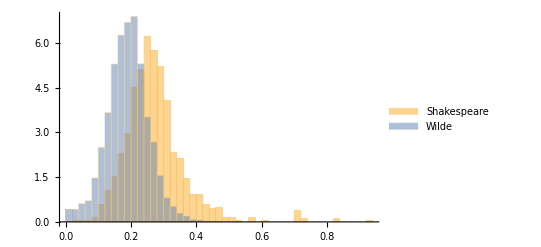

What happens to the training curve when you switch the positions of SequenceMostLayer and SequenceRestLayer in the training network? Why?

Example outputs:

NetTrain Results
summary | ,,  batches:73  rounds:1  time:25s  examples/s:97.
data | ,,  training examples:8229  validation examples:1029  processed examples:2336  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss: —   error: — 
validation | ,,  loss: —   error: — 
 | 
-Graphics-  training set	-Graphics-  validation set |

In order to classify the content, would a bidirectional model be better, identical or weaker at capturing the author specificity? Is there some task that a forward net can perform that a bidirectional one cannot achieve?

Extract the student net and modify its architecture to generate some “Shakespeare”-like verses character-wise starting by ⇥ (you can reuse the function from Generation-4.4 or Generation-4.5).

Note: Always set a maximum generation length limit to avoid an infinite loop with no termination!

Hint: Use NetExtract to extract part of a NetGraph.

Example outputs:

Oth. Know?
Are the King call'd you?

Thou Reigne Othello, 'tis not a heartine! No I, Sir
Fit, the Letter that Arters stand-booked winge my Neuer shall; go by the question to be
Laerosome Loues, in fea

Can you modify it to stop after generating one verse or one line exactly?

Example outputs:

Rod. Iago

Oth. What?
Why? Oh mine Clowde were ere that
I am kist'd From what may toward later: Newes rocke these Fortune,
And shake of him; are these deary Articles is indeed no most right
Fingers.
This sweete safety Iago dose end, being amiss'd, soules. Oh Gustio.
'Tis vnwelling in the cloud he ha's spend vp from Curiously Kinge.
Adieu: Oh Birwane!

### And with Marlowe? (Optional)

The previous test was not very significant since formatting differs as much as style. Test on a text written in a closer style: the play Edward the Second by Christopher Marlowe.

Download the text.

```mathematica
EdwardtheSecond= Import["http://www.gutenberg.org/cache/epub/20288/pg20288.txt"];
EdwardtheSecond= StringTake[EdwardtheSecond, {1384, 137905}];
```

Example outputs:

_Enter_ GAVESTON, _reading a letter._

_Gav. My father is deceas'd.  Come, Gaveston,
   And share th…

Formatting differs from Shakespeare’s plays: delete the "_" character and remove diacritics to limit test bias.

Hint: Use StringDelete and RemoveDiacritics.

Example outputs:

Enter GAVESTON, reading a letter.

Gav. My father is deceas'd.  Come, Gaveston,
   And share the kin…

Apply the following custom transformation to lessen the formatting.

Note: In the downloaded text, indentation is done with several ␣ characters instead of a ⇥.

Replace all occurrences of successive ␣ characters by a ⇥ ("	") character.

Example outputs:

Enter GAVESTON, reading a letter.

Gav. My father is deceas'd.	Come, Gaveston,
	And share the kingdo…

Split the text on every newline except when followed by a ⇥ character (indicating successive verses) using the regular expression "\n(?!\t)".

Note: The RegularExpression "\n(?!\t)" matches newline positions that are not followed by a ⇥ (this is called a look-behind).

Hint: Use StringSplit.

Example outputs:

{Enter GAVESTON, reading a letter.,«1112»,
	Sweet father, he…ief and innocency.}

Delete empty string cases.

Note: StringSplit on several newlines in a row generates meaningless empty strings. You can remove them.

Hint: Use DeleteCases.

Example outputs:

{Enter GAVESTON, reading a letter.,«1035»,
	Sweet father, he…ief and innocency.}

Split into verses using "
" as a split pattern. Delete remaining ⇥ ("	") characters.

```mathematica
newverses=Flatten@StringSplit[newsentences,"\n"];
newverses=StringDelete[newverses,"\t"];
newverses = DeleteCases[newverses, ""];
```

Example outputs:

{Enter GAVESTON, reading a letter.,«2842»,Be witness of my grief and innocency.}

Some non-ASCII characters can remain in the text. Select strings containing only printable ASCII characters.

Hint: Use PrintableASCIIQ and Select.

```mathematica
newverses = Select[newverses, PrintableASCIIQ];
```

Example outputs:

{Enter GAVESTON, reading a letter.,«2841»,Be witness of my grief and innocency.}

Add the "
" character back at verses’ ends.

Example outputs:

{Enter GAVESTON, reading a letter.
,«1035»,
	Sweet father, h…f and innocency.
}

Plot the Histogram (normalized as “PDF") from the test set of Shakespeare’s verses, Marlowe’s verses and Wilde’s sentences. Is the language model able to tell the texts apart based on their statistics?

Hint: Use the BatchSize option when evaluating the net to avoid memory exhaustion by processing all inputs at once (training used BatchSize → 32).

Example outputs:

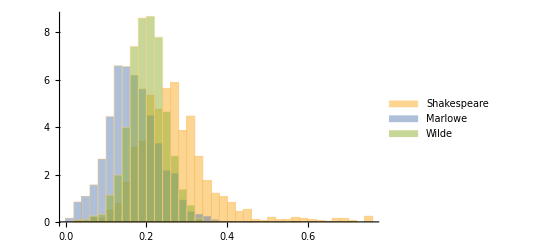

Is the language model able to tell the texts apart based on their statistics?

Which of the following statements are correct?

Marlowe’s style can be told apart from Shakespeare’s with this classifier.

Artificial intelligence proved Wilde’s style to be closer to Shakespeare’s than Marlowe’s.

The classifier can tell text from the training corpus apart from other text, and Marlowe’s verses are unlikely to be extracted from Othello, Hamlet or Macbeth.